```mathematica
Needs["MaTeX`"];
fontSize=18;
SetOptions[MaTeX,FontSize->fontSize];
SetOptions[Plot,BaseStyle->{FontSize->fontSize,FontFamily->"Times New Roman"}];
SetOptions[ListPlot,BaseStyle->{FontSize->fontSize,FontFamily->"Times New Roman"}];
SetOptions[ListDensityPlot,BaseStyle->{FontSize->fontSize,FontFamily->"Times New Roman"}];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];
Off[General::munfl](*switch off annoying warning about numbers like Exp[-800]*)
```

```mathematica
NbosTrunc=200;(*truncation of the bosonic Hilbert space;*)

b=Table[If[j==i+1,√i//N,0],{i,1,NbosTrunc},{j,1,NbosTrunc}];(*bosonic annihilation op acting in the photonic Hilbert space*)
b†=Transpose[b];(*bosonic creation op acting in the photonic Hilbert space*)
bNumOp=b†.b;
identityOp=IdentityMatrix[NbosTrunc];
bCommutator=b.b†-b†.b;
```

## for 0-junction (at ϕ_ext=π -10^-3) we get (at ϕ_ext=π +10^-3 the flux and the current would have the opposite sign -- instability):

## uncomment printing plots to track the convergence of the self-consistent loop

```mathematica
NumStepsForConvergence=50;

EC=1;
EL=0.5;
EJ=2;
coeffECoverEL=1/(√2)(EC/EL)^(1/4);
ϕext=π-10^-3;
HrfMF0=2 √(EC EL)bNumOp-2EL ϕext 1/(√2)(EC/EL)^(1/4)(b+b†)-EJ MatrixFunction[Cos,( coeffECoverEL(b+b†))];
GS0=Eigenvectors[-HrfMF0,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
GS0=GS0/√(ConjugateTranspose[GS0].GS0);
GS0†=ConjugateTranspose[GS0];
g1min=0;
g1max=1.5;
dg1=0.025;
currents=Table[0,{g1,g1min,g1max,dg1}];
energies=Table[0,{g1,g1min,g1max,dg1}];
fluxes=Table[0,{g1,g1min,g1max,dg1}];
bCommutatorArray=Table[0,{g1,g1min,g1max,dg1}];
bNumOpArray=Table[0,{g1,g1min,g1max,dg1}];
index=1;

Do[
ϕArray=Table[0,NumStepsForConvergence];
ϕArray[[1]]=GS0†.( coeffECoverEL(b+b†)).GS0;
Do[HrfMF=HrfMF0-EL 1/(1/4+g1^2)2 g1^2 (ϕArray[[step-1]]-ϕext)( coeffECoverEL(b+b†)-ϕext identityOp);
GS=Eigenvectors[-HrfMF,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
GS=GS/√(ConjugateTranspose[GS].GS);
GS†=ConjugateTranspose[GS];
ϕArray[[step]]=coeffECoverEL GS†.((b+b†)).GS;
,{step,2,NumStepsForConvergence}];
(*Print["g1=",g1];
Print[ListPlot[Re[ϕArray]]];*)

currents[[index]]={g1,2EL(ϕArray[[NumStepsForConvergence]]-ϕext- (2 g1^2  (ϕArray[[NumStepsForConvergence]]-ϕext))/(1/4+g1^2))};
energies[[index]]={g1,GS†.HrfMF.GS};
fluxes[[index]]={g1,ϕArray[[NumStepsForConvergence]]};
bCommutatorArray[[index]]={g1,GS†.bCommutator.GS};
bNumOpArray[[index]]={g1,GS†.bNumOp.GS};
index=index+1;,{g1,g1min,g1max,dg1}]
```

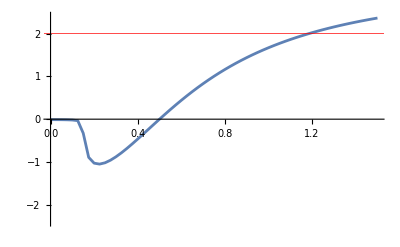

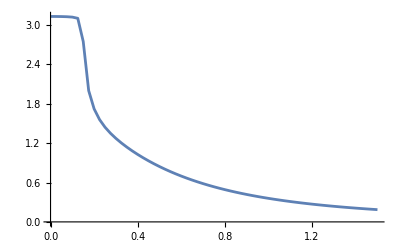

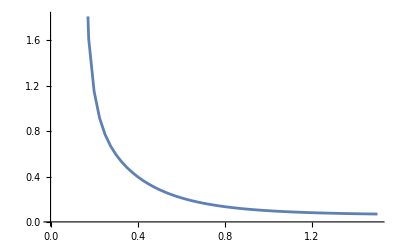

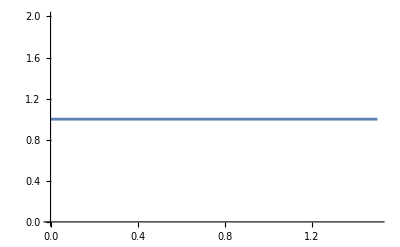

```mathematica
ListPlot[currents,AxesLabel->MaTeX@{"g_1","\\langle J\\rangle"},GridLines->{None,{Abs[EJ]}},GridLinesStyle->Red,PlotRange->{All,{-1.2Abs[EJ],1.2Abs[EJ]}},Joined->True]
ListPlot[fluxes,AxesLabel->MaTeX@{"g_1","\\langle \\Phi\\rangle"},Joined->True]
ListPlot[bNumOpArray,AxesLabel->MaTeX@{"g_1","\\langle b^\\dagger b\\rangle"},Joined->True]
ListPlot[bCommutatorArray,AxesLabel->MaTeX@{"g_1","\\langle [b,b^\\dagger]\\rangle"},Joined->True]
```

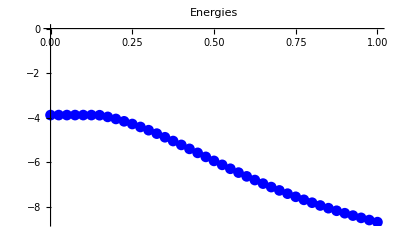

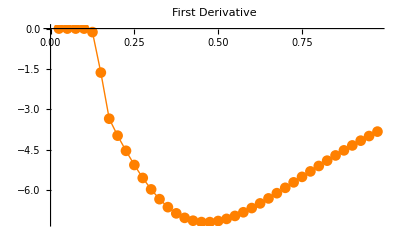

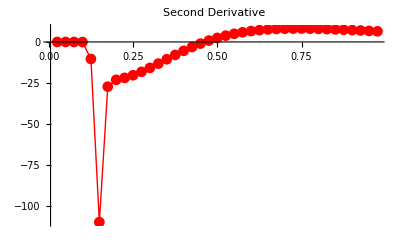

```mathematica
data=energies;
(*Extract x and y values*)
x=data[[All,1]];
y=data[[All,2]];

(*---First derivative (central difference)---*)
firstDeriv=Table[{x[[i]],(y[[i+1]]-y[[i-1]])/(x[[i+1]]-x[[i-1]])},{i,2,Length[data]-1}];

(*Compute approximate second derivative using finite differences*)secondDeriv=Table[{x[[i]],(y[[i+1]]-2 y[[i]]+y[[i-1]])/((x[[i+1]]-x[[i]]) (x[[i]]-x[[i-1]]))},{i,2,Length[data]-1}];

(*Original data*)
p1=ListPlot[data,Joined->True,PlotStyle->{Thick,Blue},PlotMarkers->Automatic,PlotLabel->"Energies",AxesLabel->MaTeX@{"g_1","E_\\text{GS}"}]

(*First derivative*)
p2=ListPlot[firstDeriv,Joined->True,PlotStyle->{Thick,Orange},PlotMarkers->Automatic,PlotLabel->"First Derivative",AxesLabel->MaTeX@{"g_1","\\partial E_\\text{GS}/\\partial g_1"}]

(*Second derivative*)
p3=ListPlot[secondDeriv,Joined->True,PlotStyle->{Thick,Red},PlotMarkers->Automatic,PlotLabel->"Second Derivative",AxesLabel->MaTeX@{"g_1","\\partial^2 E_\\text{GS}/\\partial g_1^2"},PlotRange->All]
```

## for π-junction (at ϕ_ext=-10^-5) we get(Critical current is shown with a red horizontal line):

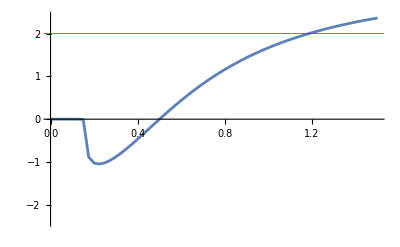

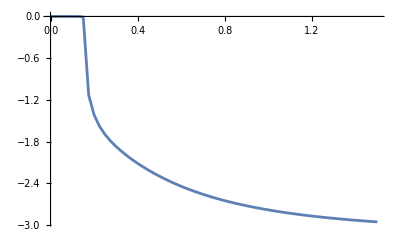

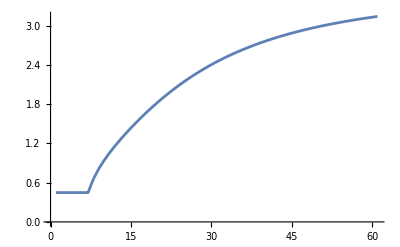

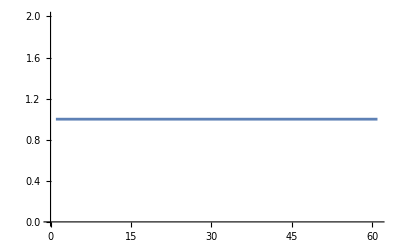

```mathematica
NumStepsForConvergence=50;

EC=1;
EL=0.5;
EJ=-2;
coeffECoverEL=1/(√2)(EC/EL)^(1/4);
ϕext=-10^-5;
HrfMF0=2 √(EC EL)bNumOp-2EL ϕext 1/(√2)(EC/EL)^(1/4)(b+b†)-EJ MatrixFunction[Cos,( coeffECoverEL(b+b†))];
GS0=Eigenvectors[-HrfMF0,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
GS0†=ConjugateTranspose[GS0];
g1min=0;
g1max=1.5;
dg1=0.025;
currents=Table[0,{g1,g1min,g1max,dg1}];
energies=Table[0,{g1,g1min,g1max,dg1}];
fluxes=Table[0,{g1,g1min,g1max,dg1}];
bCommutatorArray=Table[0,{g1,g1min,g1max,dg1}];
bNumOpArray=Table[0,{g1,g1min,g1max,dg1}];
index=1;

Do[
ϕArray=Table[0,NumStepsForConvergence];
ϕArray[[1]]=GS0†.( coeffECoverEL(b+b†)).GS0;
Do[HrfMF=HrfMF0-EL 1/(1/4+g1^2)2 g1^2 (ϕArray[[step-1]]-ϕext)( coeffECoverEL(b+b†)-ϕext identityOp);
GS=Eigenvectors[-HrfMF,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
GS=GS/√(ConjugateTranspose[GS].GS);
GS†=ConjugateTranspose[GS];
ϕArray[[step]]=coeffECoverEL GS†.((b+b†)).GS;
,{step,2,NumStepsForConvergence}];
currents[[index]]={g1,2EL(ϕArray[[NumStepsForConvergence]]-ϕext- (2 g1^2  (ϕArray[[NumStepsForConvergence]]-ϕext))/(1/4+g1^2))};
energies[[index]]={g1,GS†.HrfMF.GS};
fluxes[[index]]={g1,ϕArray[[NumStepsForConvergence]]};
bCommutatorArray[[index]]=GS†.bCommutator.GS;
bNumOpArray[[index]]=GS†.bNumOp.GS;
index=index+1;,{g1,g1min,g1max,dg1}]
ListPlot[currents,AxesLabel->MaTeX@{"g_1","\\langle J \\rangle"},GridLines->{None,{Abs[EJ]}},GridLinesStyle->Red,PlotRange->{All,{-1.2Abs[EJ],1.2Abs[EJ]}},Joined->True]
ListPlot[fluxes,AxesLabel->MaTeX@{"g_1","\\langle\\Phi \\rangle"},Joined->True]
ListPlot[bNumOpArray,AxesLabel->MaTeX@{"g_1","\\langle b^\\dagger b\\rangle"},Joined->True]
ListPlot[bCommutatorArray,AxesLabel->MaTeX@{"g_1","\\langle [b,b^\\dagger]\\rangle"},Joined->True]
```

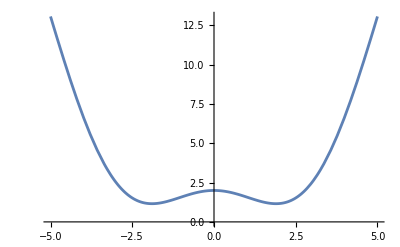

```mathematica
Plot[EL(ϕ-ϕext)^2-EJ Cos[ϕ],{ϕ,-5,5},AxesLabel->MaTeX@{"\\phi/(\\Phi_0^\\text{SC}/(2\\pi))","U(\\phi)"}]
```

## Important note: here phases (by construction are measured in unites of (Φ^SC)_0! That’s why 2π periodicity here means π-periodicity in terms of Φ_0

## for 0-junction we get the following dependence of the GS energy on the external flux (no cavity):

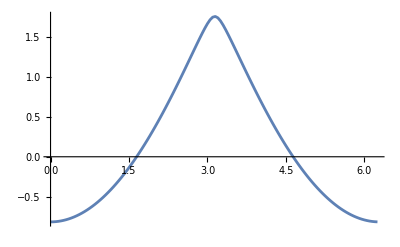

```mathematica
EC=1;
EL=0.5;
EJ=2;
coeffECoverEL=1/(√2)(EC/EL)^(1/4);
energiesArray=Table[
Hrf=EC(ⅈ 1/(√2)(EL/EC)^(1/4)(b†-b)).(ⅈ 1/(√2)(EL/EC)^(1/4)(b†-b))+EL(1/(√2)(EC/EL)^(1/4)(b+b†)-ϕext identityOp).(1/(√2)(EC/EL)^(1/4)(b+b†)-ϕext identityOp)-EJ MatrixFunction[Cos,( coeffECoverEL(b+b†))];
GS=Eigenvectors[-Hrf,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
GS=GS/√(ConjugateTranspose[GS].GS);
GS†=ConjugateTranspose[GS];
{ϕext,GS†.Hrf.GS},
{ϕext,0,2π,0.05}];
ListPlot[Re[energiesArray],AxesLabel->MaTeX@{"\\phi_\\text{ext}/(\\Phi_0^\\text{SC}/(2\\pi))","E_\\text{GS}"},Joined->True]
```

## for π- junction we get the following dependence of the GS energy on the external flux (no cavity)

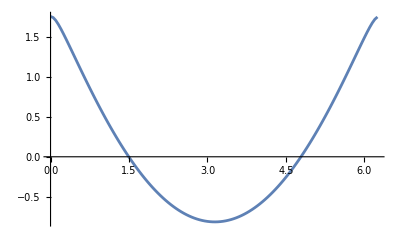

```mathematica
EC=1;
EL=0.5;
EJ=-2;
coeffECoverEL=1/(√2)(EC/EL)^(1/4);
energiesArray=Table[
Hrf=EC(ⅈ 1/(√2)(EL/EC)^(1/4)(b†-b)).(ⅈ 1/(√2)(EL/EC)^(1/4)(b†-b))+EL(1/(√2)(EC/EL)^(1/4)(b+b†)-ϕext identityOp).(1/(√2)(EC/EL)^(1/4)(b+b†)-ϕext identityOp)-EJ MatrixFunction[Cos,( coeffECoverEL(b+b†))];
GS=Eigenvectors[-Hrf,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
GS=GS/√(ConjugateTranspose[GS].GS);
GS†=ConjugateTranspose[GS];
{ϕext,GS†.Hrf.GS},
{ϕext,0,2π,0.05}];
ListPlot[Re[energiesArray],AxesLabel->MaTeX@{"\\phi_\\text{ext}/(\\Phi_0^\\text{SC}/(2\\pi))","E_\\text{GS}"},Joined->True]
```